# Epidemic Modelling - 18378566

### Abstract

This Report aims to  replicate and analyse the IEMAG SEIR model implemented to model the spread of COVID-19.

Fig 1

Fig 2

### Introduction

The figure 1 above is a flowchart describing the discrete states people are evaluated to be in in this model. SEIR itself is an acronym for the “four” states a person is can be in the model: Susceptible, Exposed, Infectious and Recovered. The first letter of each of these words corresponds to the letters in the diagram above. The model, assuming a homogeneous population then approximates statistical likelihoods of people in one group transferring to the next. For example λ is a linear function of the number of infected people, but actually represents the chance that someone is in danger of being infected based on the percentage of the population which is infected. These approximations lead to a system of first order nonlinear equations which can be solved to estimate the spread of COVID through the estimation of parameters. It is possible to solve this equations analytically but sufficient to solve them using numerical methods.

```mathematica
(*Below we define the variables involved in the series of differential equations listed above. Values are chosed to be half the expected range of each value as lsited by the report.*)
β1 =  1/(2*1.4625); (*Corresponding to a rate of infection R = 0.5*)
β2 =  1.4; (*Corresponding to a rate of infection R = 1.4*)
L = 5.0;    (*Latent period of infection*)
Ci = 5.9;    (*Averagge incubation period*)    
Dp = 7.0;    (*Average infectious period*)
h = 0.1;    (*multiplicative factor for reduction of effective transmission from the asymptomatic infected compartment Ia*)
i = 0.5;    (*multiplicative factor for reduction of effective transmission from the self-quarantine compartment Iq*)
j = 0.5;    (*multiplicative factor for reduction of effective transmission from the post-test iso- lation compartment It2*)
f = 0.5;    (*fraction of infected who are asymptomatic*)
τ = 0.75;   (*fraction of symptomatic cases that are tested*)
q = 0.125;  (*fraction of symptomatic cases that self-quarantine*)
T = 3.55;   (*average wait for test results*)
TP = 4900000; (*Total Population*)
```

### Methods

Replicating the paper, we shall implement a finite difference method to numerically approximate the integration of the equations listed in figure 2. This methods involves taking a Taylor approximation of a function and dropping all tems which are involve 2nd order derivatives or higher. As the time steps approach zero this dropping of higher order terms becomes negligible.  For this approach we construct a matrix of the relationships between derivatives of features and themselves and other features. This is based on the set of equations in fig.1. We then iterate through the finite difference method, updating the features by multiplying them by the relationship matrix and a timestep h. We then store the values as they change in a matrix, this allows Interpolation of the difference features individually and is computationally simple.

#### Testing agreement of finite difference implementation on known function

Below we will test the matrix implementation of finite difference methods.
Let F(t) = e^(2t), then F’(t)  = 2e^(2t) = 2F
Let K(t) = te^(2t), then K’(t) = e^(2t) + 2te^(2t) = F + 2K
Let U(t) = {F(t), K(t)}
Then by the finite difference formulation:

```mathematica
BC = SparseArray[{{1, 1} -> 2, {2, 1} -> 1 , {2, 2} -> 2}];
U1={Subscript[F, t], Subscript[K, t]};
U2={Subscript[F, t+1], Subscript[K, t+1]};
MatrixForm[U2]==MatrixForm[U1] + timestep.MatrixForm[BC].MatrixForm[U1]
```

(F_(1+t)
K_(1+t))==timestep.(2 | 0
1 | 2).(F_t
K_t)+(F_t
K_t)

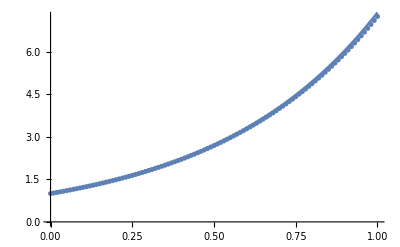

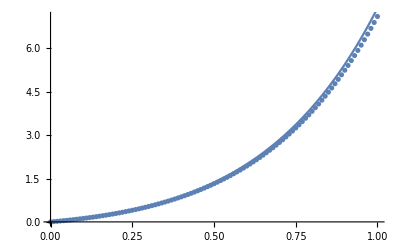

```mathematica
testarray = SparseArray[{{1, 1} -> 2, {2, 1} -> 1 , {2, 2} -> 2}];

values = {{1, 0}}; (* for t = 0 initially *)
tempvalues = {1, 0};

FDt[v_,A_, h_]:=Module[{result},
result=  v +  h*A.v;
result
];

Do[tempvalues = FDt[tempvalues, testarray, 0.01]; values= Insert[values, tempvalues, -1] , 100]

Fvalues = values[[All, 1]];
Kvalues = values[[All, 2]];

(*Plotting F(t) against the Finite difference approximation*)
Show[ListPlot[Transpose[{Range[0, 1, 0.01], Fvalues}]],Plot[Exp[2t], {t, 0, 1}] ] 

(*Plotting K(t) against the Finite difference approximation*)
Show[ListPlot[Transpose[{Range[0, 1, 0.01], Kvalues}]],Plot[t*(Exp[2t]), {t, 0, 1}] ]
```

Clearly the Finite difference method shows good agreement between the function and the approximation for a relatively high finite difference.

#### Implementing method for different values of rate of infection

In this section we assume constant rates of infection and use the equation S2 in the paper to  adapt the Force of infection λ(t). We run the numerical approximation for 30 days at time-steps of 1/1000. 
We then compare results for two difference rates of infection R = 0.5 and R = 1.4.

```mathematica
(*Iterating over a 30 day period for difference γ rates *)
notfdash[g_] := SparseArray[{{1, 1} -> -g, {2,1} -> g, {2, 2} -> -1/L, {3,2} -> f/L, {3,3} -> -1/Dp, {4,2} -> (1-f)/L, {4,4} -> -1/(Ci-L), {5,4} -> q/(Ci-L), {5,5} -> -1/(Dp-Ci+L), {6,4} -> τ/(Ci-L), {6,6} -> -1/T, {7,6} -> 1/T, {7,7} -> -1/(Dp-Ci+L), {8,4} -> (1-q-τ)/(Ci-L), {8,8} -> -1/(Dp-Ci+L), {9,3} -> 1/Dp,
{9,5} -> 1/(Dp-Ci+L), {9,7} -> 1/(Dp-Ci+L-T), {9,8} -> 1/(Dp-Ci+L), {9,9} -> 0.0 ,{10, 6} -> 1/T, {10,10} -> 0}];


(*Setting out Initial Values *)
(*S,E, Ia, Ip, Iq, It1, It2, In, R, Cn *)
(*In this context R represents the recovered patients not the Rate of infection *)
MatrixOfValuesR1 = {{4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 46.76}};
MatrixOfLambdaValues1 = {0, 47.76552*10^-6};
temp1 = {4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 47.76};

MatrixOfValuesR2 = {{4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 46.76}};
MatrixOfLambdaValues2 = {0, 117.6263736*10^-6};
temp2 = {4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 47.76};

(* Forward Difference Method *)
FD[v_, A_, t_]:=Module[{result},
result=  v +  t*A.v;
result
];

(* Updates the time continuous value of the force of infection*)
CalcLambda[x1_, x2_, x3_, x4_, x5_, x6_, B_] := Module[{result},
result=  B*(x1 + h*x2 + i*x3 + x4 + j*x5 + x6)/(4900000);
result
];

Do[temp1 = FD[temp1, notfdash[MatrixOfLambdaValues1[[-1]]], 0.001]; MatrixOfValuesR1 = Insert[MatrixOfValuesR1, temp1, -1];  MatrixOfLambdaValues1 = Append[MatrixOfLambdaValues1, CalcLambda[temp1[[4]], temp1[[3]], temp1[[5]], temp1[[6]], temp1[[7]], temp1[[8]], β1]], 30000]
Do[temp2 = FD[temp2, notfdash[MatrixOfLambdaValues2[[-1]]], 0.001]; MatrixOfValuesR2 = Insert[MatrixOfValuesR2, temp2, -1];  MatrixOfLambdaValues2 = Append[MatrixOfLambdaValues2, CalcLambda[temp2[[4]], temp2[[3]], temp2[[5]], temp2[[6]], temp2[[7]], temp2[[8]], β2]], 30000]


MatrixForm[notfdash[λ]]
```

(-λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
λ | -0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | -0.142857 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | 0 | -1.11111 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.138889 | -0.163934 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.833333 | 0 | -0.28169 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.28169 | -0.163934 | 0 | 0 | 0
0 | 0 | 0 | 0.138889 | 0 | 0 | 0 | -0.163934 | 0 | 0
0 | 0 | 0.142857 | 0 | 0.163934 | 0 | 0.392157 | 0.163934 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.28169 | 0 | 0 | 0 | 0)

Below compares graphs of the number of currently infected individuals as by the equation (11) of the paper.  The first graph shows the quick divergence of number of infected with the model using the infection rate to be 0.5 and the model using the infection rate of 1.4. Clearly the model gives higher numbers of total infected persons for higher rates of infection.

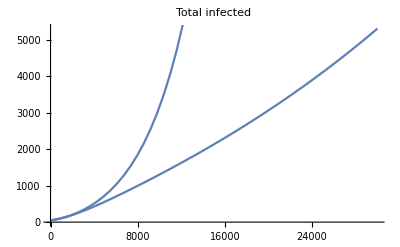

```mathematica
fR1 = Interpolation[MatrixOfValuesR1[[All, -1]]];
fR2 = Interpolation[MatrixOfValuesR2[[All, -1]]];

Show[Plot[fR1[t], {t, 1, 30000}, PlotLabel->"Total infected"], Plot[fR2[t], {t, 1, 30000}]]
```

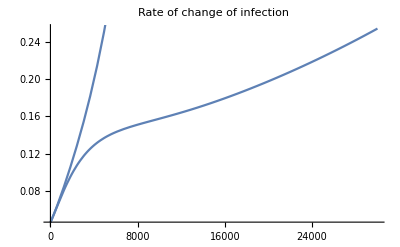

```mathematica
Show[Plot[fR1'[t], {t, 10, 30000}, PlotLabel->"Rate of change of infection"], Plot[fR2'[t], {t, 10, 30000}]]
```

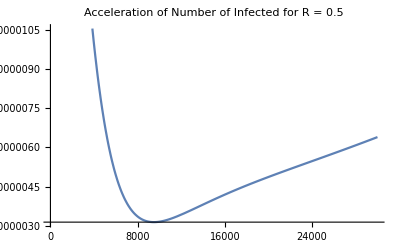

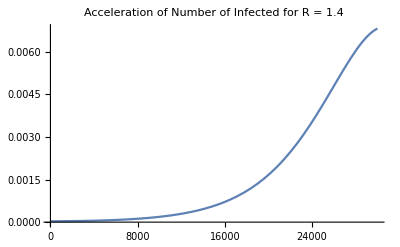

```mathematica
Plot[fR1''[t], {t, 10, 30000}, PlotLabel->"Acceleration of Number of Infected for R = 0.5"]
Plot[fR2''[t], {t, 10, 30000}, PlotLabel->"Acceleration of Number of Infected for R = 1.4"]
```

Further it can be seen that the higher rate of infection has a higher acceleration of infecting individuals than compared to the 0.5 rate. This indicated that the higher rate of infection will sustain higher infection levels for longer when compared to the lower infection rate. These are expected results and indicate the model is functioning correctly. We infer a similar relationship with the force of infection feature λ.

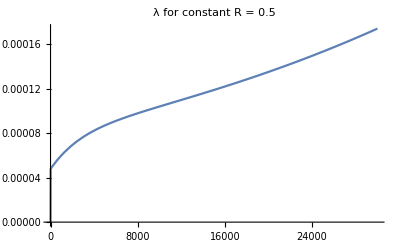

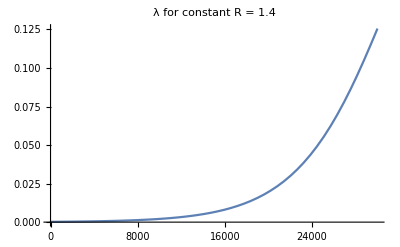

```mathematica
fλ1 = Interpolation[MatrixOfLambdaValues1];
fλ2 = Interpolation[MatrixOfLambdaValues2];

Plot[fλ1[t], {t, 1, 30000}, PlotLabel->"λ for constant R = 0.5"]
Plot[fλ2[t], {t, 1, 30000}, PlotLabel->"λ for constant R = 1.4"]
```

We can now repeat the steps above using a variable rate of infection R. This will examine the affect of “lock-downs” or to our model the rate at which people are exposed to each other and therefore the rate of infection.

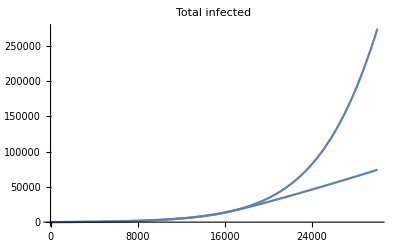

```mathematica
MatrixOfValuesR3 = {{4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 46.76}};
MatrixOfLambdaValues3 = {0, 117.6263736*10^-6};
temp3 = {4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 47.76};

(*Running half the simulation at R = 1.4 then half at R = 0.5*)
Do[temp3 = FD[temp3, notfdash[MatrixOfLambdaValues3[[-1]]], 0.001]; MatrixOfValuesR3 = Insert[MatrixOfValuesR3, temp3, -1];  MatrixOfLambdaValues3 = Append[MatrixOfLambdaValues3, CalcLambda[temp3[[4]], temp3[[3]], temp3[[5]], temp3[[6]], temp3[[7]], temp3[[8]], β2]], 15000]
Do[temp3 = FD[temp3, notfdash[MatrixOfLambdaValues3[[-1]]], 0.001]; MatrixOfValuesR3 = Insert[MatrixOfValuesR3, temp3, -1];  MatrixOfLambdaValues3 = Append[MatrixOfLambdaValues3, CalcLambda[temp3[[4]], temp3[[3]], temp3[[5]], temp3[[6]], temp3[[7]], temp3[[8]], β1]], 15000]

fR3 = Interpolation[MatrixOfValuesR3[[All, -1]]];
Show[Plot[fR2[t], {t, 1, 30000}, PlotLabel->"Total infected"], Plot[fR3[t], {t, 1, 30000}]]
```

Clearly inducing a lockdown at day 15 of a 30 day outbreak results in a massive reduction in the number of infections as predicted by the model.

#### Implementing vaccinations

Given the nature of the model it is trivially easy to implement vaccinations to the model. WE simply adjust  the model  to take away a set amount of people from the susceptible population per timestep

```mathematica
(* Assuming 2000 vaccinations per day *)
MatrixOfValuesR4 = {{4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 46.76}};
MatrixOfLambdaValues4 = {0, 47.76552*10^-6};
temp4 = {4899000, 2672, 166, 166, 166, 166, 166, 170, 1, 47.76};

Do[temp4[[1]] = temp4[[1]] -2; temp4 = FD[temp4, notfdash[MatrixOfLambdaValues4[[-1]]], 0.001]; MatrixOfValuesR4 = Insert[MatrixOfValuesR4, temp4, -1];  MatrixOfLambdaValues4 = Append[MatrixOfLambdaValues4, CalcLambda[temp4[[4]], temp4[[3]], temp4[[5]], temp4[[6]], temp4[[7]], temp4[[8]], β1]], 30000]

fR4 = Interpolation[MatrixOfValuesR4[[All, -1]]];
```

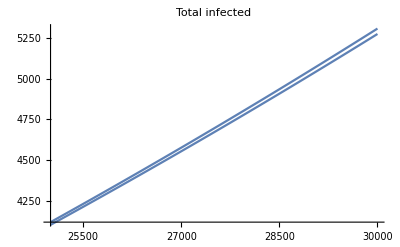

4.88157×10^6 : Total number of susceptible people after 30 days given no vaccinations

4.8218×10^6 : Total number of susceptible people after 30 days given 2000 vaccinations per day

```mathematica
Show[Plot[fR1[t], {t, 25000, 30000}, PlotLabel->"Total infected"], Plot[fR4[t], {t, 25000, 30000}]]

Print[temp1[[1]], " : Total number of susceptible people after 30 days given no vaccinations"]
Print[temp4[[1]], " : Total number of susceptible people after 30 days given 2000 vaccinations per day"]
```

Given only a 30 day simulation period the number of total infected is not significantly reduced. However given in reality the vaccines were prioritised to those most vulnerable and this likely would have a dramatic 
reduction in the number of deaths as caused by the virus. This could be more effectively simulated if the  groups incorporated age as a feature affecting transmissibility and mortality.

### Conclusions

The IEMAG SEIR model sufficiently models COVID19 infections and is flexible enough to allow for variations such as vaccination and lock-downs or other methods which can be easily incorporated into the model. It is likely given sufficient parameter tuning this model could be used to accurately model any number of scenarios.